```mathematica
Numerics;
(* Import files for lambda/4 thickness at 615 nm (starting on substrate)*)

fiberlist = Import["/Users/ejanitz/Dropbox/McGill/Project/Cavity/Cavity Simulations/New Mirror Coating Simulations/fiber_coating.csv"];
flatslist = Import["/Users/ejanitz/Dropbox/McGill/Project/Cavity/Cavity Simulations/New Mirror Coating Simulations/flats_coating.csv"];

(* tables for thicknesses *)
fiberthick = Table[0,Length[fiberlist]];
flatsthick = Table[0,Length[flatslist]];
nfiber = Table[0,Length[fiberlist]];
nflats = Table[0,Length[flatslist]];

nhim = 3.1*10^-6;
nlim = 3.1*10^-6; 
ndim = 0*10^-6;
σd =1.5*10^-10;
λt = 615*10^-9;
c = 2.99792458*10^8;
R0=45*10^-6;

γ = 1/(6*10^-9);
γs =2*Pi*5.22*10^12;

dimplant = 125*10^-9;
dimplant1 = (125-20)*10^-9;
dimplant2 = (125+20)*10^-9;
dimplant11 = (125-40)*10^-9;
dimplant22 = (125+40)*10^-9;

Ed35p3 = 0.81613760507;
Ed54p7 = 0.57785762507; 

nh=2.125-I*nhim;
nl=1.482-I*nlim;
nd = 2.417-I*ndim;
na=1;
ns=1.4633;

M[n1_, n2_]:= ({{(Re[n1]+Re[n2])/(2 Re[n2]), (-Re[n1]+Re[n2])/(2 Re[n2])}, {(-Re[n1]+Re[n2])/(2 Re[n2]), (Re[n1]+Re[n2])/(2 Re[n2])}}); (* This is going from n1 into n2 *)

L[λ_,n_,d_]:={{Exp[-I*2*Pi*n*d/λ], 0},{0, Exp[I*2*Pi*n*d/λ]}}

Calculate air and diamond parameters;
r12[λ_,σ_]:=(Re[na]-Re[nd])/(Re[na]+Re[nd])*Exp[-2*(2*Pi*σ/λ)^2];
t12[λ_,σ_]:=2*Re[na]/(Re[na]+Re[nd])*Exp[-1/2*(2*Pi*σ*(1-Re[nd])/λ)^2];
r21[λ_,σ_]:=(Re[nd]-Re[na])/(Re[na]+Re[nd])*Exp[-2*(2*Pi*σ*Re[nd]/λ)^2];
t21[λ_,σ_]:=(2*Re[nd])/(Re[na]+Re[nd])*Exp[-1/2*(2*Pi*σ*(Re[nd]-1)/λ)^2];

r34[λ_,σ_]:=r21[λ,σ];
t34[λ_,σ_]:=t21[λ,σ];
r43[λ_,σ_]:=r12[λ,σ];
t43[λ_,σ_]:=t12[λ,σ];

Dad[λ_,σ_]:={{t12[λ,σ]-(r12[λ,σ]*r21[λ,σ])/t21[λ,σ], r21[λ,σ]/t21[λ,σ]},{-r12[λ,σ]/t21[λ,σ], 1/t21[λ,σ]}};
Dda[λ_,σ_]:={{t34[λ,σ]-(r34[λ,σ]*r43[λ,σ])/t43[λ,σ], r43[λ,σ]/t43[λ,σ]},{-r34[λ,σ]/t43[λ,σ], 1/t43[λ,σ]}};
```

1

7.15×10^-7

1.50732×10^9

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Set::pkspec1: The expression j cannot be used as a part specification.

1.6619×10^-11

18111.8

Table::iterb: Iterator {x,dimplant11,dimplant22,7.15×10^-11} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

2

7.3×10^-7

1.76985×10^9

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindFit::sszero will be suppressed during this calculation.

Set::pkspec1: The expression j cannot be used as a part specification.

General::stop: Further output of Set::pkspec1 will be suppressed during this calculation.

2.6192×10^-11

11492.1

3

$Aborted

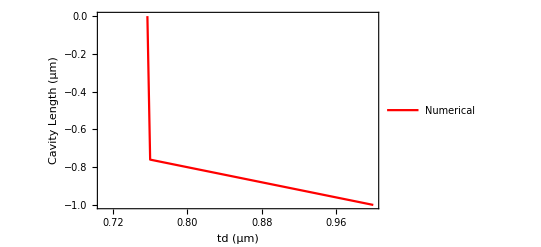

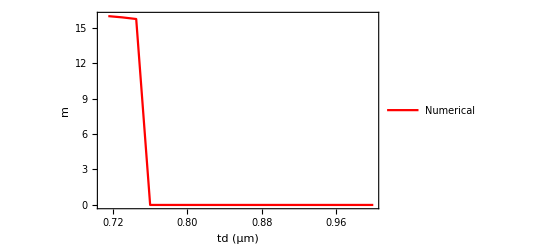

```mathematica
Calculating Mirror Reflectivities;

For[i=1,i<(Length[fiberlist])+1,i++,
	If[fiberlist[[i,2]]=="SiO2",n=nl,n=nh];
	fiberthick[[i]]=λt/(Re[n]*4)*fiberlist[[i,3]];
	nfiber[[i]]=n;
]

For[i=1,i<(Length[flatslist])+1,i++,
	If[flatslist[[i,2]]=="SiO2",n=nl,n=nh];
	flatsthick[[i]]=λt/(Re[n]*4)*flatslist[[i,3]];
	nflats[[i]] = n;
]

(* define wavelenth range for simulations*)
λtest=602*10^-9;
ftest = c/λtest;

mmax = 1;
kmax =20;
mtarget = 16;

tdmin =0.7*10^-6;
tdmax =1*10^-6;

tdvec = Table[tdmin+(tdmax-tdmin)*k/kmax,{k,kmax}];
Lvec = Table[0,{k,kmax}];
mvec = Table[0,{k,kmax}];
FSRvec =Table[0,{k,kmax}];
fwidthVec=Table[0,{k,kmax}];
EVec=Table[0,{k,kmax}];
normVec=Table[0,{k,kmax}];
Fpvec=Table[0,{k,kmax}];
Fpvec1=Table[0,{k,kmax}];
Fpvec2=Table[0,{k,kmax}];
Fpvec11=Table[0,{k,kmax}];
Fpvec22=Table[0,{k,kmax}];
RVec=Table[0,{k,kmax}];
RVec1=Table[0,{k,kmax}];
RVec2=Table[0,{k,kmax}];
RVec11=Table[0,{k,kmax}];
RVec22=Table[0,{k,kmax}];

gvec=Table[0,{k,kmax}];
gvec1=Table[0,{k,kmax}];
gvec2=Table[0,{k,kmax}];
gvec11=Table[0,{k,kmax}];
gvec22=Table[0,{k,kmax}];


Vvec=Table[0,{k,kmax}];
Vvec1=Table[0,{k,kmax}];
Vvec2=Table[0,{k,kmax}];
Vvec11=Table[0,{k,kmax}];
Vvec22=Table[0,{k,kmax}];

Evec=Table[0,{k,kmax}];
Evec1=Table[0,{k,kmax}];
Evec2=Table[0,{k,kmax}];
Evec11=Table[0,{k,kmax}];
Evec22=Table[0,{k,kmax}];

Mfiber= M[nh,ns];
	For[i=1,i<(Length[fiberlist])+1,i++,
		If[fiberlist[[i,2]]=="SiO2",Mfiber=Simplify[Mfiber.L[λtest,nfiber[[i]],fiberthick[[i]]].M[nh,nl]]];
		If[fiberlist[[i,2]]=="Ta2O5" && i≠Length[fiberlist],Mfiber=Simplify[Mfiber.L[λtest,nfiber[[i]],fiberthick[[i]]].M[nl,nh]]];
		If[fiberlist[[i,2]]=="Ta2O5" && i==Length[fiberlist],Mfiber=Simplify[Mfiber.L[λtest,nfiber[[i]],fiberthick[[i]]].M[na,nh]]];
	];

	Mflatsinv= M[nl,na];
	For[i=Length[flatslist],i>0,i--,
		If[flatslist[[i,2]]=="SiO2",Mflatsinv=Simplify[Mflatsinv.L[λtest,nflats[[i]],flatsthick[[i]]].M[nh,nl]]];
		If[flatslist[[i,2]]=="Ta2O5" && i≠1,Mflatsinv=Simplify[Mflatsinv.L[λtest,nflats[[i]],flatsthick[[i]]].M[nl,nh]]];
		If[flatslist[[i,2]]=="Ta2O5" && i==1,Mflatsinv=Simplify[Mflatsinv.L[λtest,nflats[[i]],flatsthick[[i]]].M[ns,nh]]];
	];

For[k=1,k<kmax+1,k++,(* here i'm iterating over diamond thickness td - λtest is fixed *)

	Print[k];
	(* starting guess for length *)
	Lmin =(mtarget+1/2)*λtest/2-(nd-1)*tdvec[[k]];

	Stest[Ltest_,λ_] := Mfiber.L[λ,na,(Ltest-tdvec[[k]])].Dda[λtest,σd].L[λ,nd,tdvec[[k]]].Dad[λtest,σd].Mflatsinv;
          (* this is the transmitted field Z1 *)
	Gtest[Ltest_,freq_] := Stest[Ltest,c/freq][[1,1]]-Stest[Ltest,c/freq][[1,2]]*Stest[Ltest,c/freq][[2,1]]/Stest[Ltest,c/freq][[2,2]];
	(* calculate the reflected field A2 *)
	A2test[Ltest_,freq_]:=-Stest[Ltest,c/freq][[2,1]]/Stest[Ltest,c/freq][[2,2]];

	(* find resonance *)
	Ltest = L/.NMaximize[Abs[FullSimplify[Gtest[L,ftest]]]^2,{L,Lmin-λtest/4,Lmin}][[2]];

	(* Print["this is resonant reflection ",Abs[A2test[Ltest,ftest]]^2];
	Print["this is resonant transmission ",Abs[Gtest[Ltest,ftest]]^2]; *)
	
	(* populate length and m vector *)
	Lvec[[k]]=Ltest;	
	mvec[[k]]=2*((nd-1)*tdvec[[k]]+Ltest)/λtest-1/2;

	(* now in frequency *)
	FSRtest = c/(2*(Ltest-tdvec[[k]]+Re[nd]*tdvec[[k]]));
	fHighF = Table[i,{i,ftest-FSRtest/2000,ftest+FSRtest/2000,FSRtest/1000000}];
	fTHigh = Table[Abs[Gtest[Ltest,i]]^2,{i,ftest-FSRtest/2000,ftest+FSRtest/2000,FSRtest/1000000}];
	fHighFDat = Transpose[{fHighF,fTHigh}];
	(*Print[ListLinePlot[Transpose[{(fHighF-λtest)*10^9,fTHigh}],PlotRange->Full,AxesLabel->{"laser wavelength (nm)","T"}]];*)

	af=Max[fTHigh]-Min[fTHigh]; (* amplitude *)
	yf = Min[fTHigh]; (* offset *)
	x0f = fHighF[[( Position[fTHigh,Max[fTHigh]][[1]])[[1]]]]; (* center position *)
	bguessf = 2*Abs[x0f-fHighF[[(Position[fTHigh,Nearest[fTHigh,Min[fTHigh]+af/2][[1]]][[1]])[[1]]]]]; (* guess at width*)

	fFit = a*(b/2)^2/((x-x0)^2+(b/2)^2)+y;
	fpeakW  = Quiet[b/. FindFit[fHighFDat,fFit,{{b,bguessf},{x0,x0f},{a,af},{y,yf}},x][[1]]];
	fwidthVec[[k]] = fpeakW;
	fTHighFit = Table[af*(fpeakW/2)^2/((fHighF[[i]]-x0f)^2+(fpeakW/2)^2)+yf,{i,Length[fHighF]}];

	FSRmin = f/.NMaximize[{Abs[FullSimplify[Gtest[Ltest,f]]]^2,f>x0f-1.6*FSRtest&&f<x0f-0.4*FSRtest},f][[2]];
	FSRmax = f/.NMaximize[{Abs[FullSimplify[Gtest[Ltest,f]]]^2,f>x0f+0.4*FSRtest&&f<x0f+1.6*FSRtest},f][[2]];
	FSRvec[[k]]= ((fpeakW-FSRmin)+(FSRmax-fpeakW))/2;
	(* Print[Plot[Abs[Gtest[Ltest,f]]^2,{f,x0f-1.5*FSRtest,x0f+1.5*FSRtest},PlotRange->Full]];  *)	(*Print[ListLinePlot[{ Transpose[{(fHighF-x0f),fTHigh}],Transpose[{(fHighF-x0f),fTHighFit}]},PlotRange->Full,    PlotLabel->"Resonance in frequency",AxesLabel->{"f (Hz)","T"}]]; *)
Print[tdvec[[k]]];
Print[fpeakW];

		(* finesse in length *)
		lHighF = Table[i,{i,Ltest-λtest/2/5000,Ltest+λtest/2/5000,λtest/2/1000000}];
		lTHigh = Table[Abs[Gtest[i,ftest]]^2,{i,Ltest-λtest/2/5000,Ltest+λtest/2/5000,λtest/2/1000000}];
		lHighFDat = Transpose[{lHighF,lTHigh}];
	
		(* first in length*)
		al=Max[lTHigh]-Min[lTHigh]; (* amplitude *)
		yl = Min[lTHigh]; (* offset *)
		x0l = lHighF[[( Position[lTHigh,Max[lTHigh]][[1]])[[1]]]]; (* center position *)
		bguessl = 2*Abs[x0l-lHighF[[(Position[lTHigh,Nearest[lTHigh,Min[lTHigh]+al/2][[1]]][[1]])[[1]]]]]; (* guess at width*)

		lFit = a*(b/2)^2/((x-x0)^2+(b/2)^2)+y;
		lpeakW  = b/. FindFit[lHighFDat,lFit,{{b,bguessl},{x0,x0l},{a,al},{y,yl}},x][[1]];
		Ltest = x0/.FindFit[lHighFDat,lFit,{{x0,x0l},{b,bguessl},{a,al},{y,yl}},x][[1]];
		Lvec[[j]]=Ltest;
		lwidthVec[[j]] = lpeakW;
                     Print[lpeakW];
		lTHighFit = Table[al*(lpeakW/2)^2/((lHighF[[i]]-Ltest)^2+(lpeakW/2)^2)+yl,{i,Length[lHighF]}];		(*Print[ListLinePlot[{ Transpose[{(lHighF-Ltest)*10^9,lTHigh}],Transpose[{(lHighF-Ltest)*10^9,lTHighFit}]},PlotRange->Full,AxesLabel->{"cavity length (nm)","T"},PlotLabel->N[λtest*10^9]]]; *)
	Print[λtest/2/lpeakW];

	z02=td*(1-1/nd)/.λ->c/ν/.ta->(L-td)/.{td->tdvec[[k]],L->Ltest,ν->ftest};
	w01= Sqrt[λ/Pi]*((ta+td/nd)*(R0-(ta+td/nd)))^(1/4)/.λ->c/ν/.ta->(L-td)/.{td->tdvec[[k]],L->Ltest,ν->ftest};

	(* determine electric field in diamond *)
	Evals =Dda[λtest,σd].L[λtest,nd,tdvec[[k]]].Dad[λtest,σd].Mflatsinv .{{1},{A2test[Ltest,ftest] }};
	E1 =Evals[[1]];
	E2 = Evals[[2]];
	
	Dvals =L[λtest,nd,tdvec[[k]]].Dad[λtest,σd].Mflatsinv.{{1 },{A2test[Ltest,ftest] }};
	D1 =Dvals[[1]];
	D2 = Dvals[[2]];
	
	Cvals = Dad[λtest,σd].Mflatsinv.{{1 },{A2test[Ltest,ftest] }};
	C1 =Cvals[[1]];
	C2 = Cvals[[2]];

	(* Evals =Dda[λtest,σd].L[λtest,nd,tdvec[[k]]].Dad[λtest,σd].Mflatsinv .{{1},{0}};
	E1 =Evals[[1]];
	E2 = Evals[[2]];
	
	Dvals =L[λtest,nd,tdvec[[k]]].Dad[λtest,σd].Mflatsinv.{{1 },{0}};
	D1 =Dvals[[1]];
	D2 = Dvals[[2]];
	
	Cvals = Dad[λtest,σd].Mflatsinv.{{1 },{0}};
	C1 =Cvals[[1]];
	C2 = Cvals[[2]]; *)

	(* Determine the max electric field in diamond *)
	(*dEfield = Max[Table[Re[C1*ⅇ^(-ⅈ x*(2*π*nd/λtest))+C2*ⅇ^(+ⅈ x*(2*π*nd/λtest))][[1]],{x,0,tdvec[[k]],tdvec[[k]]/10000}]];*)
	dEfield = Abs[Re[(C1*ⅇ^(-ⅈ dimplant*(2*π*nd/λtest))+C2*ⅇ^(+ⅈ dimplant*(2*π*nd/λtest)))][[1]]];
	dEfield1 = Min[Abs[Table[Re[C1*ⅇ^(-ⅈ x*(2*π*nd/λtest))+C2*ⅇ^(+ⅈ x*(2*π*nd/λtest))][[1]],{x,dimplant1,dimplant2,tdvec[[k]]/10000}]]];
	dEfield2 = Max[Abs[Table[Re[C1*ⅇ^(-ⅈ x*(2*π*nd/λtest))+C2*ⅇ^(+ⅈ x*(2*π*nd/λtest))][[1]],{x,dimplant1,dimplant2,tdvec[[k]]/10000}]]];
	dEfield11 = Min[Abs[Table[Re[C1*ⅇ^(-ⅈ x*(2*π*nd/λtest))+C2*ⅇ^(+ⅈ x*(2*π*nd/λtest))][[1]],{x,dimplant11,dimplant22,tdvec[[k]]/10000}]]];
	dEfield22 = Max[Abs[Table[Re[C1*ⅇ^(-ⅈ x*(2*π*nd/λtest))+C2*ⅇ^(+ⅈ x*(2*π*nd/λtest))][[1]],{x,dimplant11,dimplant22,tdvec[[k]]/10000}]]];
	(*dEfield1 = Re[(C1*ⅇ^(-ⅈ dimplant1*(2*π*nd/λtest))+C2*ⅇ^(+ⅈ dimplant1*(2*π*nd/λtest)))][[1]];
	dEfield2 = Re[(C1*ⅇ^(-ⅈ dimplant2*(2*π*nd/λtest))+C2*ⅇ^(+ⅈ dimplant2*(2*π*nd/λtest)))][[1]];*)
	EVec[[k]] = dEfield; *)

	field100 = Re[nd]^2*Re[Quiet[NIntegrate[(Re[C1*ⅇ^(-ⅈ x*(2*π*nd/λtest))+C2*ⅇ^(ⅈ x*(2*π*nd/λtest))])^2*Pi*w01^2/2,{x,0,tdvec[[k]]},AccuracyGoal->8]]];
	field200 = Re[Quiet[NIntegrate[(Re[E1*ⅇ^(-ⅈ( x-tdvec[[k]])*(2*π/λtest))+E2*ⅇ^(ⅈ (x-tdvec[[k]])*(2*π/λtest))])^2*Pi*w01^2/2,{x,tdvec[[k]],Ltest},AccuracyGoal->8]]];

	(* I need to add a section where I integrate the field inside the mirror coatings... *)

	fieldfiber = 0;
	For[i=1,i<(Length[fiberlist])+1,i++,
		If[fiberlist[[i,2]]=="SiO2",fieldfiber=fieldfiber+0];
		If[fiberlist[[i,2]]=="Ta2O5" && i≠Length[fiberlist],fieldfiber=fieldfiber+0];
		If[fiberlist[[i,2]]=="Ta2O5" && i==Length[fiberlist],fieldfiber=fieldfiber+0];
	];

	fieldflat = 0;
	For[i=Length[flatslist],i>0,i--,
		If[flatslist[[i,2]]=="SiO2",fieldflat = fieldflat + 0;];
		If[flatslist[[i,2]]=="Ta2O5" && i≠1,fieldflat = fieldflat + 0;];
		If[flatslist[[i,2]]=="Ta2O5" && i==1,fieldflat = fieldflat + 0;];
	];

	norm00 = field100+field200+fieldflat+fieldfiber;
	normVec[[k]] = norm00[[1]];

	V = norm00/(Re[nd]^2*Abs[dEfield]^2);
	V1 = norm00/(Re[nd]^2*Abs[dEfield1]^2);
	V2 = norm00/(Re[nd]^2*Abs[dEfield2]^2);
	V11 = norm00/(Re[nd]^2*Abs[dEfield11]^2);
	V22 = norm00/(Re[nd]^2*Abs[dEfield22]^2);
	Q=c/(λtest*fpeakW);
	gtest = Sqrt[(3*c*γ*λtest^2)/(8*Pi*Re[nd]^3*V)][[1]];
	gtest1 = Sqrt[(3*c*γ*λtest^2)/(8*Pi*Re[nd]^3*V1)][[1]];
	gtest2 = Sqrt[(3*c*γ*λtest^2)/(8*Pi*Re[nd]^3*V2)][[1]];
	gtest11 = Sqrt[(3*c*γ*λtest^2)/(8*Pi*Re[nd]^3*V11)][[1]];
	gtest22 = Sqrt[(3*c*γ*λtest^2)/(8*Pi*Re[nd]^3*V22)][[1]];

	(*Fpvec[[k]]=4*gtest^2/(γ*2*Pi*fpeakW);
	Fpvec1[[k]]=4*gtest1^2/(γ*2*Pi*fpeakW);
	Fpvec2[[k]]=4*gtest2^2/(γ*2*Pi*fpeakW);*)

	Fpvec[[k]]=3/(4*Pi^2)*(λtest/nd)^3*(Q/V);
	Fpvec1[[k]]=3/(4*Pi^2)*(λtest/nd)^3*(Q/V1);
	Fpvec2[[k]]=3/(4*Pi^2)*(λtest/nd)^3*(Q/V2);
	Fpvec11[[k]]=3/(4*Pi^2)*(λtest/nd)^3*(Q/V11);
	Fpvec22[[k]]=3/(4*Pi^2)*(λtest/nd)^3*(Q/V22);

	gvec[[k]]=gtest;
	gvec1[[k]]=gtest1;
	gvec2[[k]]=gtest2;
	gvec11[[k]]=gtest11;
	gvec22[[k]]=gtest22;


	Vvec[[k]]=V;
	Vvec1[[k]]=V1;
	Vvec2[[k]]=V2;
	Vvec11[[k]]=V11;
	Vvec22[[k]]=V22;

	Evec[[k]]=dEfield;
	Evec1[[k]]=dEfield1;
	Evec2[[k]]=dEfield2;
	Evec11[[k]]=dEfield11;
	Evec22[[k]]=dEfield22;

	RVec[[k]]=4*gtest^2/γs;
	RVec1[[k]]=4*gtest1^2/γs;
	RVec2[[k]]=4*gtest2^2/γs;
	RVec11[[k]]=4*gtest11^2/γs;
	RVec22[[k]]=4*gtest22^2/γs;


];
 
ListLinePlot[{Transpose[{tdvec*10^6,(Lvec-tdvec)*10^6}]},AxesLabel->{"td","ta"},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},(*PlotMarkers->{Automatic,12},*)FrameLabel->{"td (μm)","Cavity Length (μm)"},FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotStyle->Red,PlotLegends->{"Numerical"}] 

ListLinePlot[{Transpose[{tdvec*10^6,mvec}]},AxesLabel->{"laser λ (nm)","cavity L (um)"},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},(*PlotMarkers->{Automatic,12},*)FrameLabel->{"td (μm)","m"},FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotStyle->Red,PlotLegends->{"Numerical"}] 

(*ListLinePlot[{Transpose[{tdvec*10^6,βVec*100}],Transpose[{tdvec*10^6,βVec1*100}],Transpose[{tdvec*10^6,βVec2*100}]},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},(*PlotMarkers->{Automatic,12},*)FrameLabel->{"td (μm)","β (%)"},FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotLegends->{"target","-straggle","+straggle"}] *)
```